```mathematica
(* compare the dimensional and nondimensional formulas using the exponential force-position function *)
```

## Assumptions

In Charlie’s book, there is a given motor species where a motor attaches at position x=A and pulls the filaments in the direction x=-∞. Therefore, dx/dt =-v, where v is the velocity of motion when the motor pushes in the preferred direction. If we include the negative sign in v and assume v<0 in the preferred direction, the problem is identical to that introduced in Fa et al 2017, and follows.

```mathematica
(* default parameters *)
pi3Val=α/β;
pi4Val=γ*A;
pi5Val=γ(B-A);
(*F0=α p1 n0/(α+β);*)
f0Rule={F0->(Exp[γ A]-1)α p1 n0/(α+β)};
pi6Val=F0/(6 Pi Rp mu)/(β/γ);
(* collect all parameters in a single rule set *)
ruleNonDim2Dim={pi3->α/β,pi4->γ A,pi5->γ(B-A),pi6->F0/(6 π Rp mu)/(β/γ),k->p1*γ};
rulePeskin={n0->100,α->14,β->126,A->5,B->5.5,γ->0.322,p1->4,k->4*.322,Rp->.96,mu->1.2,phi1Val->0.5,
ζVal->1};
ruleDim={n0->100,α->10,β->100,A->5,B->5.5,γ->0.322,p1->4,k->4*.322,Rp->.96,mu->1.2,phi1Val->0.5,
ζVal->0};
ruleDim2Val=ruleDim;
```

## Population Distributions

### Preferred direction

```mathematica
pPrefTemp=DSolve[{U ϕ'[z]==-β ϕ[z],ϕ[A]==ϕ0},ϕ[z],z][[All,1,2]]
```

DSolve::dsfun: -(c ⅇ^(-((-A+z) β)/U) α β)/(U (α+c β)) cannot be used as a function.

Part::partd: Part specification DSolve[{True,-(c α β)/(U (α+Times[«2»]))==ϕ0},-(c ⅇ^(-((-A+z) β)/U) α β)/(U (α+c β)),z]⟦All,1,2⟧ is longer than depth of object.

DSolve[{True,-(c α β)/(U (α+c β))==ϕ0},-(c ⅇ^(-((-A+z) β)/U) α β)/(U (α+c β)),z]⟦All,1,2⟧

```mathematica
θPref=Integrate[pPrefTemp,{z,-Infinity,A},Assumptions->U<0&&β>0]
```

Integrate[DSolve[{True,-(c α β)/(U (α+c β))==ϕ0},-(c ⅇ^(-((-A+z) β)/U) α β)/(U (α+c β)),z]⟦All,1,2⟧,{z,-∞,A},Assumptions→U<0&&β>0]

```mathematica
(* find constant in previous line *)
c1Pref=Solve[α(1-θPref)==-U ϕ0,ϕ0][[All,1,2]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Part::partd: Part specification Solve[α (1-Integrate[Part[«4»],{«3»},Rule[«2»]])==-U ϕ0,ϕ0]⟦All,1,2⟧ is longer than depth of object.

$Aborted

```mathematica
(* full phi in preferred direction *)
pPref[z_]=FullSimplify[pPrefTemp/.ϕ0->c1Pref][[1]]
```

{-(ⅇ^(((A-z) β)/U) α β)/(U (α+β))}

```mathematica
tempreplace={α->14,β->126,A->5,U->-50};
```

```mathematica
(*Integrate[pPref[z],{z,-Infinity,5}]*)
```

```mathematica
(ⅇ^(((-5+A) β)/U) α)/(α+β)/.tempreplace
```

1/10

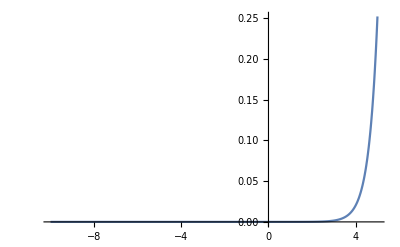

```mathematica
Plot[pPref[z]/.tempreplace,{z,-10,5},PlotRange->All]
```

### Non-preferred direction

```mathematica
pNonPrefTemp=DSolve[{U ϕ'[z]==-β ϕ[z],ϕ[A]==ϕ0},ϕ[z],z][[All,1,2]]
```

{ⅇ^((A β)/U-(z β)/U) ϕ0}

```mathematica
θNonPref=Integrate[pNonPrefTemp,{z,A,B},Assumptions->U>0&&β>0]
```

{-((-1+ⅇ^(((A-B) β)/U)) U ϕ0)/β}

```mathematica
(* find constant in previous line *)
c1NonPref=Solve[α(1-θNonPref)==U ϕ0,ϕ0][[All,1,2]]
```

{-(α β)/(U (-α+ⅇ^(((A-B) β)/U) α-β))}

```mathematica
(* full phi in non-preferred direction *)
pNonPref[z_]=FullSimplify[pNonPrefTemp/.ϕ0->c1NonPref][[1]]
```

{(ⅇ^(((A-z) β)/U) α β)/(U (α-ⅇ^(((A-B) β)/U) α+β))}

```mathematica
-(ⅇ^(((A-z) β)/U) α β)/(U (α+β))
```

-(ⅇ^(((A-z) β)/U) α β)/(U (α+β))

```mathematica
FullSimplify[pNonPref[B]]
FullSimplify[(α-θNonPref[[1]]*(α+β)/.ϕ0->c1NonPref)/U]
```

{(α β)/(-U α+ⅇ^(((-A+B) β)/U) U (α+β))}

{(α β)/(-U α+ⅇ^(((-A+B) β)/U) U (α+β))}

```mathematica
Simplify[pNonPref[B]]
```

{(ⅇ^(((A-B) β)/U) α β)/(U (α-ⅇ^(((A-B) β)/U) α+β))}

```mathematica
tempreplace2={α->14,β->126,A->5,B->5.5,U->50};
```

```mathematica
Integrate[pNonPref[z],{z,A,B}]
```

{1-β/(α-ⅇ^(((A-B) β)/U) α+β)}

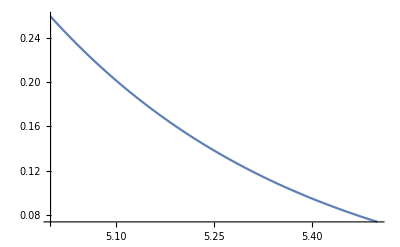

```mathematica
(*Plot[{pPref[z]}/.α->1/.β->1/.A->5/.U->-10,{z,-100,5},PlotRange->All]*)
Plot[{pNonPref[z](*,(α β c)/(-U(α+β c))Exp[-β(z-A)/U]/.c->1-Exp[β(B-A)/U]*)}/.tempreplace2,{z,5,5.5},PlotRange->All]
```

Note that the equation above is written
ϕ(z) = (α β)/(U(α c+β))exp[-β(z-A)/U], c=1-exp[-β(B-A)/U]
while Equation 32 in Fai et al is written
ϕ(z) = (α β c)/(-U(α+β c))exp[-β(z-A)/U], c=1-exp[β(B-A)/U]

```mathematica
pTFai[z]=(α β c)/(-U(α+β c))Exp[-β(z-A)/U]/.c->1-Exp[β(B-A)/U];
```

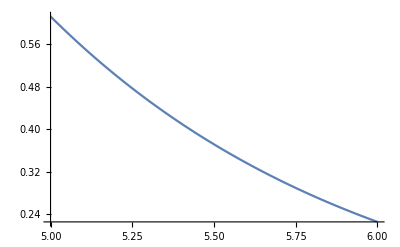

```mathematica
(* plot of the comparison between the population curve defined in Fai et al and the population curve re-derived above *)
rule1={B->6,A->5,α->1,β->1,U->1};
Plot[{pNonPref[z]/.rule1,pTFai[z]/.rule1},{z,5,6}]
```

```mathematica
(* compute total fraction of attached motors in non-preferred v, for the formula above and the one written in fai et al *)
N[Integrate[pNonPref[z],{z,5,Infinity}]/.B->6/.A->5/.α->1/.β->1/.U->1]
N[Integrate[pTFai[z],{z,5,6}]/.B->6/.A->5/.α->1/.β->1/.U->1]
```

{0.6127}

-1.51217

## Forces (exponential and linear)

Double checking Equation 34 in Fai et al. 2017

```mathematica
(* force exerted by an individual motor. Motors that attach at z=A prefer to push down, so force is negative *)
p[z_]:=-p1 (Exp[γ z]-1);
pLinear[z_]:=-k z;
```

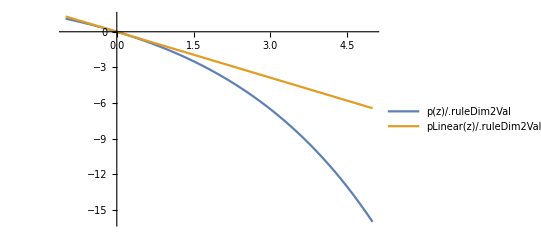

```mathematica
Plot[{p[z]/.ruleDim2Val,pLinear[z]/.ruleDim2Val},{z,-1,5},PlotLegends->"Expressions"]
```

### Preferred direction

```mathematica
(* get force-velocity when position is < A, i.e., v < 0 for exponential and linear force velocity *)
fPrefExp[U_]=FullSimplify[Integrate[n0 p[z]pPref[z],{z,-Infinity,A},Assumptions->U<0&&β>0&&γ>0]][[1]]
fPrefLin[U_]=FullSimplify[Integrate[n0 pLinear[z]pPref[z],{z,-Infinity,A},Assumptions->U<0&&β>0]][[1]]
```

-(n0 p1 α ((-1+ⅇ^(A γ)) β+U γ))/((α+β) (β-U γ))

-(k n0 α (U+A β))/(β (α+β))

```mathematica
(* the above expression coincides with Fai et al *)
```

### Non-preferred direction

```mathematica
(* get force-velocity when position >A and < B, i.e., v >0. Perform integral in Eq (33) to get Eq 34 *)
fNonPrefExp[U_]=FullSimplify[Integrate[n0 p[z]pNonPref[z],{z,A,B},Assumptions->U>0&&β>0&&γ>0]][[1]]
fNonPrefLin[U_]=FullSimplify[Integrate[n0 pLinear[z]pNonPref[z],{z,A,B},Assumptions->U>0&&β>0&&γ>0]][[1]]
```

n0 p1 (1+(β (-ⅇ^(A γ) α+ⅇ^(((A-B) β)/U+B γ) α-β+U γ))/((α-ⅇ^(((A-B) β)/U) α+β) (β-U γ)))

-(k n0 α (U+A β-ⅇ^(((A-B) β)/U) (U+B β)))/(β (α-ⅇ^(((A-B) β)/U) α+β))

### Function for downwards-pushing motors

```mathematica
fLinear[U_]:=If[U>0,fNonPrefLin[U],fPrefLin[U]];
fExp[U_]:=If[U>0,fNonPrefExp[U],fPrefExp[U]];
```

### Comparison plots between lienar force-position and exponential force-position

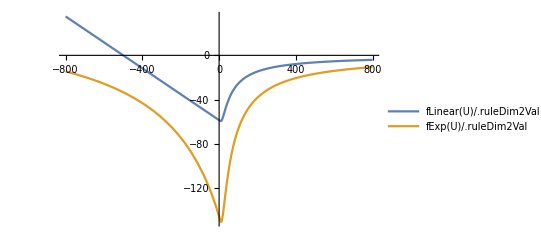

```mathematica
Plot[{fLinear[U]/.ruleDim2Val,fExp[U]/.ruleDim2Val},{U,-800,800},PlotLegends->"Expressions"]
```

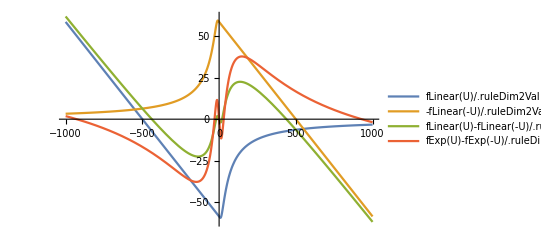

```mathematica
Plot[{fLinear[U]/.ruleDim2Val,-fLinear[-U]/.ruleDim2Val,fLinear[U]-fLinear[-U]/.ruleDim2Val,fExp[U]-fExp[-U]/.ruleDim2Val},{U,-1000,1000},PlotLegends->"Expressions"]
```

For some calculations, the derivative of the force function is needed.

## Nondimensional verification

Formulas were derived by hand. Verified below.

```mathematica
fNonPrefND[U_]:=-(pi3+1)/(pi3(1-Exp[-pi5/(pi6 U)])+1) (Exp[pi4](1-Exp[pi5] Exp[-pi5/(pi6 U)])-(1-pi6 U)(1-Exp[-pi5/(pi6 U)]))/((1-pi6  U) (Exp[pi4]-1));
fPrefND[U_]:=-(1+pi6 U(Exp[pi4]-1)^-1)/(1-pi6 U);
(*Subscript[F, A][U_]:=If[U>0,FAPlus[U],If[U==0,-1+2 phi1,FAMinus[U]]];*)
fND[U_]:=If[U≥0,fNonPrefND[U],fPrefND[U]];
(*FAMPlus[U_]:=(1-pi6 U(Exp[pi4]-1)^-1)/(1+pi6 U);
FAMMinus[U_]:=(pi3+1)/(pi3(1-Exp[pi5/(pi6 U)])+1) (Exp[pi4](1-Exp[pi5] Exp[pi5/(pi6 U)])-(1+pi6 U)(1-Exp[pi5/(pi6 U)]))/((1+pi6  U) (Exp[pi4]-1));
Fm[U_]:=If[U≥0,FAMPlus[U],FAMMinus[U]];*)
```

```mathematica
fNonPrefND[100]/.ruleNonDim2Dim/.ruleDim
```

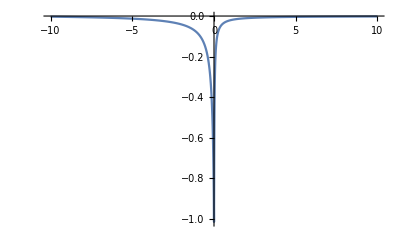

```mathematica
Plot[fND[U]/.pi3->1/.pi4->5/.pi5->.1/.pi6->10,{U,-10,10},PlotRange->All]
```

```mathematica
(* U < 0 *)
s=Solve[-phi fNonPrefND[U]+(1-phi) fPrefND[U]==0,pi4];
FullSimplify[Exp[pi4/.s]]
```

{ConditionalExpression[-((pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (1+2 pi3)) (-1+pi6 U))/(pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (pi3+ⅇ^pi5 (1+pi3))), C[1]∈ℤ]}

```mathematica
FortranForm[((pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (1+2 pi3)) (-1+pi6 U))/(pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (pi3+ⅇ^pi5 (1+pi3)))]
```

((pi3 + E**(pi5/(pi6*U))*(-1 + 2*phi)*(1 + pi3) - phi*(1 + 2*pi3))*
     -    (-1 + pi6*U))/
     -  (pi3 + E**(pi5/(pi6*U))*(-1 + 2*phi)*(1 + pi3) - 
     -    phi*(pi3 + E**pi5*(1 + pi3)))

```mathematica
s=Solve[-phi fPrefND[U]+(1-phi) fNonPrefND[U]==0,pi4];
FullSimplify[Exp[pi4/.s]]
```

{ConditionalExpression[((1+pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (1+2 pi3)) (-1+pi6 U))/(phi pi3+ⅇ^pi5 (-1+phi) (1+pi3)-ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)), C[1]∈ℤ]}

```mathematica
FortranForm[((1+pi3+ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3)-phi (1+2 pi3)) (-1+pi6 U))/(phi pi3+ⅇ^pi5 (-1+phi) (1+pi3)-ⅇ^(pi5/(pi6 U)) (-1+2 phi) (1+pi3))]
```

((1 + pi3 + E**(pi5/(pi6*U))*(-1 + 2*phi)*(1 + pi3) - phi*(1 + 2*pi3))*
     -    (-1 + pi6*U))/
     -  (phi*pi3 + E**pi5*(-1 + phi)*(1 + pi3) - 
     -    E**(pi5/(pi6*U))*(-1 + 2*phi)*(1 + pi3))

### Verify for preferred direction

```mathematica
prefND2D=FullSimplify[fPrefND[U/(F0/(6 Pi Rp mu))]*F0/.ruleNonDim2Dim/.f0Rule]
```

-(n0 p1 α ((-1+ⅇ^(A γ)) β+U γ))/((α+β) (β-U γ))

```mathematica
FullSimplify[fPrefExp[U]]
```

-(n0 p1 α ((-1+ⅇ^(A γ)) β+U γ))/((α+β) (β-U γ))

```mathematica
Reduce[prefND2D== fPrefExp[U]]
```

True

### Verify for non-preferred direction

```mathematica
nonPrefND2D=FullSimplify[fNonPrefND[U/(F0/(6 Pi Rp mu))]*F0/.ruleNonDim2Dim/.f0Rule]
```

(n0 p1 α ((-1+ⅇ^(B γ)) β+U γ+ⅇ^(((-A+B) β)/U) (β-ⅇ^(A γ) β-U γ)))/((-α+ⅇ^(((-A+B) β)/U) (α+β)) (β-U γ))

```mathematica
FullSimplify[fNonPrefExp[U]]
```

n0 p1 (1+(β (-ⅇ^(A γ) α+ⅇ^(((A-B) β)/U+B γ) α-β+U γ))/((α-ⅇ^(((A-B) β)/U) α+β) (β-U γ)))

```mathematica
Reduce[nonPrefND2D== fNonPrefExp[U]]
```

True